```mathematica
Plot3D[Sin[x]*Sin[y]+0.05*((x+1)^2+(y-1)^2 + Abs[x]+Abs[y]), {x, -5, 6},{y, -5, 6}]
```

-Graphics3D-

```mathematica
f[x_] := 0.25x(x-1)(x+2)(x-2)(x+1)
```

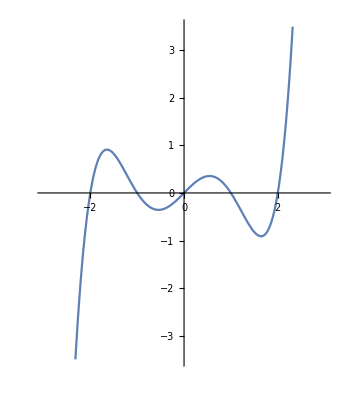

```mathematica
Plot[f[x], {x, -3, 3}, AspectRatio->Automatic]
```

```mathematica
Animate[Show[Plot[f[x], {x, -3, 3}, AspectRatio->Automatic], Graphics[{Black, PointSize[.03], Point[{t,f[t]}]}]],{t, -1.4, -.5}, AnimationRunning->False]
```

```mathematica
f'[x]
```

0.25 (-2+x) (-1+x) x (1+x)+0.25 (-2+x) (-1+x) x (2+x)+0.25 (-2+x) (-1+x) (1+x) (2+x)+0.25 (-2+x) x (1+x) (2+x)+0.25 (-1+x) x (1+x) (2+x)